```mathematica
1+1
```

2

## Initialization

```mathematica
<<"C:\\Users\\fsiano\\work\\dev\\workspace\\AD\\AD\\Kernel\\AD.m"
```

## Γ matrix and related

```mathematica
g={{1, a, b}, {a, 1, c},{b, c,1}} ;
```

```mathematica
g // MatrixForm
```

(1 | a | b
a | 1 | c
b | c | 1)

```mathematica
es=Eigensystem[g, Cubics->True];
es={es[[1]], Normalize[#] & /@ es[[2]]};
Dot[Transpose[es[[2]]],DiagonalMatrix[es[[1]]],es[[2]]][[1,1]] //Simplify
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

$Aborted

```mathematica
Dot[es[[2]],DiagonalMatrix[es[[1]]],Transpose[es[[2]]]] //FullSimplify
```

$Aborted

```mathematica
Module[{a=4, b=3, c=5},
es= Eigensystem[{{1, a, b}, {a, 1, c},{b, c,1}}];
es={es[[1]], Normalize[#] & /@ es[[2]]};
Dot[Transpose[es[[2]]],DiagonalMatrix[es[[1]]],es[[2]]] //Simplify
]
```

{{1,4,3},{4,1,5},{3,5,1}}

## Checks

```mathematica
vDate={2015, 4, 13, 0, 0, 0};
expDate={2016,4, 13, 0, 0, 0};
settDate={2016,4, 13, 0, 0, 0};
barrierStartDate={2015, 6, 1, 0,0,0};
barrierEndDate={2015, 8, 31, 0,0,0};
```

```mathematica
barrierOption[1,{17.0,0.05,0.3},{50.0,0.05 10^-9, 0.03 10^-9},0.25,0.1,{QuantityMagnitude[DateDifference[vDate, barrierStartDate, "Day"]]/365.25,QuantityMagnitude[DateDifference[vDate, barrierEndDate, "Day"]]/365.25,10 10^-9,55},40,QuantityMagnitude[DateDifference[vDate, expDate, "Day"]]/365.25,QuantityMagnitude[DateDifference[vDate, settDate, "Day"]]/365.25,{-2,2}] /. BarrierOption`Private`n -> 0
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

0.00807697

```mathematica
cp=1;
{sUnd,sYield,sVol}={50., 0., 0.35};
{bUnd,bYield,bVol}={50., 0., 0.23};
corr=-0.98;
intRate=0.025;
{t1,t2,bLow,bHigh}={1/365.242, 1., 35., 55.};
strike=50.;
t=1.;ts=1.;{nMin,nMax}={-5,5};
```

```mathematica
doubleKnockOutOutsideBarrierOptionValue[cp,{sUnd,sYield,sVol},{bUnd,bYield,bVol},corr,intRate,{t1,t2,bLow,bHigh},strike,t,ts,{nMin,nMax}]
```

2.05871

```mathematica
doubleKnockOutOutsideBarrierOptionValue[cp,{sUnd,sYield,sVol},{bUnd,bYield,bVol},corr,intRate,{t/2,t2,bLow,bHigh},strike,t,ts,{nMin,nMax}]
```

2.76486

```mathematica
doubleKnockOutOutsideBarrierOptionValue[cp,{sUnd,sYield,sVol},{bUnd,bYield,bVol},corr,fd[intRate, <|"intRate"-> 1|>],{t/2,t2,bLow,bHigh},strike,t,ts,{nMin,nMax}]
```

Merge::list1: The argument propagatefd[Apply[Times][ReplacePart[{CDF[MultinormalDistribution[«2»],{«3»}]-CDF[«2»]-CDF[«2»]+CDF[MultinormalDistribution[«2»],{«3»}],ⅇ^(-1.37287 BarrierOption`Private`n$4657)},1→#1]]&,CDF[MultinormalDistribution[{0,0,0},{{1,0.98,0.692965},{«1»},{«1»}}],«1»],-CDF[MultinormalDistribution[{0,0,0},{{1,0.98,0.692965},{0.98,1,0.707107},{0.692965,0.707107,1}}],{fd[0.35+2.85714 Plus[«2»],<|intRate→2.85714|>],fd[0.343+4.34783 Plus[«2»],<|intRate→-4.34783|>],fd[0.833034,<|intRate→-3.07438|>]}]] is not a valid list of Associations or rules or lists of rules.

Merge::list1: The argument propagatefd[Apply[Times][ReplacePart[{-1,CDF[MultinormalDistribution[«2»],{«3»}]-CDF[«2»]-CDF[«2»]+CDF[MultinormalDistribution[«2»],{«3»}],ⅇ^(-1.51871 Plus[«2»])},2→#1]]&,CDF[MultinormalDistribution[{0,0,0},{{1,0.98,0.692965},{0.98,1,«19»},«1»}],{«1»}],-CDF[MultinormalDistribution[{0,0,0},{{1,0.98,0.692965},{0.98,1,0.707107},{0.692965,0.707107,1}}],{fd[0.35+2.85714 Plus[«2»],<|intRate→2.85714|>],fd[0.343+4.34783 Plus[«2»],<|intRate→-4.34783|>],fd[0.833034,<|intRate→-3.07438|>]}]] is not a valid list of Associations or rules or lists of rules.

Merge::list1: The argument propagatefd[Apply[Plus][ReplacePart[{-ⅇ^Times[«2»] (CDF[«2»]+Times[«2»]+Times[«2»]+CDF[«2»]),ⅇ^Times[«2»] (CDF[«2»]+Times[«2»]+Times[«2»]+CDF[«2»])},1→#1]]&,-ⅇ^(«1») «1»,Merge[{propagatefd[Apply[Times][ReplacePart[{«3»},Rule[«2»]]]&,CDF[MultinormalDistribution[{0,0,0},{{«3»},{«3»},{«3»}}],{fd[Plus[«2»],<|intRate→2.85714|>],fd[Plus[«2»],<|intRate→-4.34783|>],fd[-1.94611,<|intRate→-3.07438|>]}],-CDF[MultinormalDistribution[{«3»},{«3»}],{fd[«2»],fd[«2»],fd[«2»]}]],«11»,<|intRate→18.9036 ⅇ^(-1.51871 («20»-«19» «28»)) (0.19062-0.90397 «28») («1»)|>},Total]] is not a valid list of Associations or rules or lists of rules.

General::stop: Further output of Merge::list1 will be suppressed during this calculation.

$Aborted

```mathematica
Attributes[CDF]
```

{Protected,ReadProtected}

```mathematica
Attributes[PDF]
```

{Protected,ReadProtected}

## Port to Python

```mathematica
{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}} //MatrixForm
```

(1 | -corr cp √(t2/t) | -corr cp √(t1/t)
-corr cp √(t2/t) | 1 | √(t1/t2)
-corr cp √(t1/t) | √(t1/t2) | 1)

```mathematica
value=barrierOption[cp,{sUnd,sYield,sVol},{bUnd,bYield,bVol},corr,intRate,{t1,t2,bLow,bHigh},strike,t, ts,{nMin,nMax}] /. BarrierOption`Private`n  -> n;
```

```mathematica
value
```

cp (ⅇ^(-sYield t) sUnd (ⅇ^((2 n (-bVol^2/2-bYield+intRate+bVol corr sVol) (Log[bHigh/bUnd]+Log[bLow/bUnd]))/bVol^2) (CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+(2 corr n sVol (Log[bHigh/bUnd]+Log[bLow/bUnd]))/bVol-Log[strike/sUnd])/(sVol √t)),-corr sVol √t2+((bVol^2/2+bYield-intRate) t2+Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),-corr sVol √t1+((bVol^2/2+bYield-intRate) t1+Log[bHigh/bUnd])/(bVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+(2 corr n sVol (Log[bHigh/bUnd]+Log[bLow/bUnd]))/bVol-Log[strike/sUnd])/(sVol √t)),-corr sVol √t2+((bVol^2/2+bYield-intRate) t2+Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),-corr sVol √t1+((bVol^2/2+bYield-intRate) t1+Log[bLow/bUnd])/(bVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+(2 corr n sVol (Log[bHigh/bUnd]+Log[bLow/bUnd]))/bVol-Log[strike/sUnd])/(sVol √t)),-corr sVol √t2+((bVol^2/2+bYield-intRate) t2+Log[bLow/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),-corr sVol √t1+((bVol^2/2+bYield-intRate) t1+Log[bHigh/bUnd])/(bVol √t1)}]+CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+(2 corr n sVol (Log[bHigh/bUnd]+Log[bLow/bUnd]))/bVol-Log[strike/sUnd])/(sVol √t)),-corr sVol √t2+((bVol^2/2+bYield-intRate) t2+Log[bLow/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),-corr sVol √t1+((bVol^2/2+bYield-intRate) t1+Log[bLow/bUnd])/(bVol √t1)}])-ⅇ^(((-bVol^2/2-bYield+intRate+bVol corr sVol) (2 Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd])))/bVol^2) (CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+(corr sVol (2 Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd])))/bVol-Log[strike/sUnd])/(sVol √t)),-corr sVol √t2+((bVol^2/2+bYield-intRate) t2-Log[bHigh/bUnd]+2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),-corr sVol √t1+((bVol^2/2+bYield-intRate) t1+Log[bHigh/bUnd])/(bVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+(corr sVol (2 Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd])))/bVol-Log[strike/sUnd])/(sVol √t)),-corr sVol √t2+((bVol^2/2+bYield-intRate) t2-Log[bHigh/bUnd]+2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),-corr sVol √t1+((bVol^2/2+bYield-intRate) t1+Log[bLow/bUnd])/(bVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+(corr sVol (2 Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd])))/bVol-Log[strike/sUnd])/(sVol √t)),-corr sVol √t2+((bVol^2/2+bYield-intRate) t2-2 Log[bHigh/bUnd]+Log[bLow/bUnd]+2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),-corr sVol √t1+((bVol^2/2+bYield-intRate) t1+Log[bHigh/bUnd])/(bVol √t1)}]+CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+(corr sVol (2 Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd])))/bVol-Log[strike/sUnd])/(sVol √t)),-corr sVol √t2+((bVol^2/2+bYield-intRate) t2-2 Log[bHigh/bUnd]+Log[bLow/bUnd]+2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),-corr sVol √t1+((bVol^2/2+bYield-intRate) t1+Log[bLow/bUnd])/(bVol √t1)}]))-ⅇ^(-intRate t) strike (ⅇ^((2 (-bVol^2/2-bYield+intRate) n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/bVol^2) (CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{(cp ((intRate-sVol^2/2-sYield) t+(2 corr n sVol (Log[bHigh/bUnd]+Log[bLow/bUnd]))/bVol-Log[strike/sUnd]))/(sVol √t),((bVol^2/2+bYield-intRate) t2+Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),((bVol^2/2+bYield-intRate) t1+Log[bHigh/bUnd])/(bVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{(cp ((intRate-sVol^2/2-sYield) t+(2 corr n sVol (Log[bHigh/bUnd]+Log[bLow/bUnd]))/bVol-Log[strike/sUnd]))/(sVol √t),((bVol^2/2+bYield-intRate) t2+Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),((bVol^2/2+bYield-intRate) t1+Log[bLow/bUnd])/(bVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{(cp ((intRate-sVol^2/2-sYield) t+(2 corr n sVol (Log[bHigh/bUnd]+Log[bLow/bUnd]))/bVol-Log[strike/sUnd]))/(sVol √t),((bVol^2/2+bYield-intRate) t2+Log[bLow/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),((bVol^2/2+bYield-intRate) t1+Log[bHigh/bUnd])/(bVol √t1)}]+CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{(cp ((intRate-sVol^2/2-sYield) t+(2 corr n sVol (Log[bHigh/bUnd]+Log[bLow/bUnd]))/bVol-Log[strike/sUnd]))/(sVol √t),((bVol^2/2+bYield-intRate) t2+Log[bLow/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),((bVol^2/2+bYield-intRate) t1+Log[bLow/bUnd])/(bVol √t1)}])-ⅇ^(((-bVol^2/2-bYield+intRate) (2 Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd])))/bVol^2) (CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{(cp ((intRate-sVol^2/2-sYield) t+(corr sVol (2 Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd])))/bVol-Log[strike/sUnd]))/(sVol √t),((bVol^2/2+bYield-intRate) t2-Log[bHigh/bUnd]+2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),((bVol^2/2+bYield-intRate) t1+Log[bHigh/bUnd])/(bVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{(cp ((intRate-sVol^2/2-sYield) t+(corr sVol (2 Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd])))/bVol-Log[strike/sUnd]))/(sVol √t),((bVol^2/2+bYield-intRate) t2-Log[bHigh/bUnd]+2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),((bVol^2/2+bYield-intRate) t1+Log[bLow/bUnd])/(bVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{(cp ((intRate-sVol^2/2-sYield) t+(corr sVol (2 Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd])))/bVol-Log[strike/sUnd]))/(sVol √t),((bVol^2/2+bYield-intRate) t2-2 Log[bHigh/bUnd]+Log[bLow/bUnd]+2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),((bVol^2/2+bYield-intRate) t1+Log[bHigh/bUnd])/(bVol √t1)}]+CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{(cp ((intRate-sVol^2/2-sYield) t+(corr sVol (2 Log[bHigh/bUnd]-2 n (Log[bHigh/bUnd]+Log[bLow/bUnd])))/bVol-Log[strike/sUnd]))/(sVol √t),((bVol^2/2+bYield-intRate) t2-2 Log[bHigh/bUnd]+Log[bLow/bUnd]+2 n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),((bVol^2/2+bYield-intRate) t1+Log[bLow/bUnd])/(bVol √t1)}])))

## Junk

```mathematica
gammaMat={{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}};
```

```mathematica
Limit[gammaMat, t1->0]
```

{{1,-corr cp √(t2/t),0},{-corr cp √(t2/t),1,0},{0,0,1}}

```mathematica
Limit[CDF[MultinormalDistribution[{0, 0, 0}, IdentityMatrix[3]], {0.1,0.2 ,x}], x->Infinity]
```

0.312701

```mathematica
FullSimplify[PDF[MultinormalDistribution[{0,0,0}, {{1,-corr cp √(t2/t),0},{-corr cp √(t2/t),1,0},{0,0,1}}], {x,y,z}]]==FullSimplify[PDF[MultinormalDistribution[{0,0}, {{1,-corr cp √(t2/t)},{-corr cp √(t2/t),1}}], {x,y}] PDF[NormalDistribution[0,1], z]]
```

True

```mathematica
test=CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+(2 corr BarrierOption`Private`n sVol (Log[bHigh/bUnd]+Log[bLow/bUnd]))/bVol-Log[strike/sUnd])/(sVol √t)),-corr sVol √t2+((bVol^2/2+bYield-intRate) t2+Log[bHigh/bUnd]-2 BarrierOption`Private`n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),-corr sVol √t1+((bVol^2/2+bYield-intRate) t1+Log[bHigh/bUnd])/(bVol √t1)}]
```

CDF[MultinormalDistribution[{0,0,0},{{1,-corr cp √(t2/t),-corr cp √(t1/t)},{-corr cp √(t2/t),1,√(t1/t2)},{-corr cp √(t1/t),√(t1/t2),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+(2 corr BarrierOption`Private`n sVol (Log[bHigh/bUnd]+Log[bLow/bUnd]))/bVol-Log[strike/sUnd])/(sVol √t)),-corr sVol √t2+((bVol^2/2+bYield-intRate) t2+Log[bHigh/bUnd]-2 BarrierOption`Private`n (Log[bHigh/bUnd]+Log[bLow/bUnd]))/(bVol √t2),-corr sVol √t1+((bVol^2/2+bYield-intRate) t1+Log[bHigh/bUnd])/(bVol √t1)}]

```mathematica
subs={CDF[MultinormalDistribution[mean_, cov_], point_]-> mvnscdf[mean, cov, point]}
```

MultinormalDistribution::arprm: -- Message text not found -- (mean_) (1) (MultinormalDistribution[mean_, cov_])

{CDF[MultinormalDistribution[mean_,cov_],point_]→mvnscdf[mean,cov,point]}

```mathematica
xxx=barrierOption[1,{s,0,vol},{s,0,vol},corr,intRate,{t1,t2,bLow,bHigh},strike,t,ts,{nMin,nMax}] //Simplify
```

```mathematica
phi[{1.23}, {{0.45}}][{0.56}]
```

0.158951

```mathematica
phi[{1.23}, {{0.45}}][{fd[0.56, <|"x1"->1|>]}]
```

fd[0.158951,<|x1→0.36115|>]

```mathematica
phi[{1.23}, {{fd[0.45, <|"vol1"->1|>]}}][{fd[0.56, <|"x1"->1|>]}]
```

fd[0.158951,<|vol1→0.268856,x1→0.36115|>]

```mathematica
phi[{1.23, 0.321}, {{0.45 0.45, 0.98 0.45 0.32}, {0.98 0.45 0.32, 0.32 0.32}}][{0.56, -0.12}]
```

0.0630841

```mathematica
phi[{1.23, 0.321}, {{0.45 0.45, 0.98 0.45 0.32}, {0.98 0.45 0.32, 0.32 0.32}}][{fd[0.56, <|"x1"->1|>], fd[-0.12, <|"x2"->1|>]}]
```

CDF[MultinormalDistribution[{0,0},{{1.,0.98},{0.98,1.}}],{fd[-1.48889,<|x1→2.22222|>],fd[-1.37813,<|x2→3.125|>]}]

```mathematica
smallPhi[{0.1}, {{0.45}}, {-1.032}]
```

0.240796

```mathematica
smallPhi[{fd[0.1, <|"m1"->1|>]}, {{fd[0.45, <|"vol1"->1|>]}}, {fd[-1.032, <|"x1"->1|>]}]
```

fd[0.240796,<|x1→0.605736,m1→-0.605736,vol1→0.761881|>]

```mathematica
smallPhi[{0.1, -0.3}, {{0.45 0.45, 0.98 0.45 0.33}, {0.98 0.45 0.33, 0.33 0.33}}, {0.032, -0.0547}]
```

0.000218176

```mathematica
smallPhi[{fd[0.1, <|"mu1"->1|>], fd[-0.3, <|"mu2"->1|>]}, {{fd[0.45, <|"vol1"->1|>]^2, fd[0.98, <|"rho12"->1|>] fd[0.45, <|"vol1"->1|>]fd[ 0.33, <|"vol2"->1|>]}, {fd[0.98, <|"rho12"->1|>] fd[0.45, <|"vol1"->1|>] fd[ 0.33, <|"vol2"->1|>],fd[ 0.33, <|"vol2"->1|>]^2}}, {fd[0.032, <|"x1"->1|>], fd[-0.0547, <|"x2"->1|>]}]
```

fd[0.000218176,<|vol2→0.0110628,vol1→0.00162731,rho12→-0.103688,x2→-0.0148827,mu2→0.0148827,mu1→-0.010769,x1→0.010769|>]

```mathematica
phi[{0.1}, {{0.45}}, {-1.032}]
```

0.0769369

```mathematica
phi[{0.1, -0.2}, {{0.45 0.45, -0.98 0.45 0.3}, {-0.98 0.45 0.3, 0.3 0.3}}, {-1.032, 0.5}]
```

0.000347151

```mathematica
phi[{fd[0.1, <|"m1"->1|>]}, {{0.45}}, {-1.032}]
```

NIntegrate::inumr: The integrand fd[1. ⅇ^(-1.11111 (-0.1+z35)^2),<|m1→2.22222 ⅇ^(-1.11111 (-0.1+z35)^2) (-0.1+z35)|>] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,-1.032}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[fd[1. ⅇ^(-1.11111 (-0.1+z35)^2),<|m1→2.22222 ⅇ^(-1.11111 (-0.1+z35)^2) (-0.1+z35)|>],{z35,-∞,-1.032}]

```mathematica
Dt[Integrate[f[t,x1,x2], {x1, lb1, ub1}, {x2, lb2, ub2}], t] // TraditionalForm
```

(ub3-lb3) (∫_lb1^ub1 (∫_lb2^ub2 f^(1,0,0)(t,x1,x2)ⅆx2-ⅆlb2/ⅆt f(t,x1,lb2)+ⅆub2/ⅆt f(t,x1,ub2))ⅆx1-ⅆlb1/ⅆt ∫_lb2^ub2 f(t,lb1,x2)ⅆx2+ⅆub1/ⅆt ∫_lb2^ub2 f(t,ub1,x2)ⅆx2)+(ⅆub3/ⅆt-ⅆlb3/ⅆt) ∫_lb1^ub1 ∫_lb2^ub2 f(t,x1,x2)ⅆx2ⅆx1

```mathematica
smallPhi[{m1, m2}, {{vol1 vol1, rho12 vol1 vol2}, {rho12 vol1 vol2, vol2 vol2}}, {x1, x2}]//Simplify
```

(ⅇ^((m2^2 vol1^2+m1^2 vol2^2+vol2^2 x1^2-2 rho12 vol1 vol2 x1 x2+vol1^2 x2^2-2 m2 vol1 (m1 rho12 vol2-rho12 vol2 x1+vol1 x2)+2 m1 vol2 (-vol2 x1+rho12 vol1 x2))/(2 (-1+rho12^2) vol1^2 vol2^2)))/(√(1-rho12^2))

```mathematica
smallPhi[{m1, m2}, {{vol1 vol1, 0 vol1 vol2}, {0 vol1 vol2, vol2 vol2}}, {x1, x2}]//Simplify
```

ⅇ^(-(m1-x1)^2/(2 vol1^2)-(m2-x2)^2/(2 vol2^2))

```mathematica
smallPhi[{m1, m2, m3}, {{vol1 vol1, rho12 vol1 vol2, rho13 vol1 vol3}, {rho12 vol1 vol2, vol2 vol2, rho23 vol2 vol3}, {rho13 vol1 vol3, rho23 vol2 vol3, vol3 vol3}}, {x1, x2, x3}]//Simplify
```

ⅇ^(-(m3^2 (-1+rho12^2) vol1^2 vol2^2+m2^2 (-1+rho13^2) vol1^2 vol3^2-m1^2 vol2^2 vol3^2+m1^2 rho23^2 vol2^2 vol3^2+2 m1 vol2^2 vol3^2 x1-2 m1 rho23^2 vol2^2 vol3^2 x1-vol2^2 vol3^2 x1^2+rho23^2 vol2^2 vol3^2 x1^2-2 m1 rho12 vol1 vol2 vol3^2 x2+2 m1 rho13 rho23 vol1 vol2 vol3^2 x2+2 rho12 vol1 vol2 vol3^2 x1 x2-2 rho13 rho23 vol1 vol2 vol3^2 x1 x2-vol1^2 vol3^2 x2^2+rho13^2 vol1^2 vol3^2 x2^2-2 m1 rho13 vol1 vol2^2 vol3 x3+2 m1 rho12 rho23 vol1 vol2^2 vol3 x3+2 rho13 vol1 vol2^2 vol3 x1 x3-2 rho12 rho23 vol1 vol2^2 vol3 x1 x3-2 rho12 rho13 vol1^2 vol2 vol3 x2 x3+2 rho23 vol1^2 vol2 vol3 x2 x3-vol1^2 vol2^2 x3^2+rho12^2 vol1^2 vol2^2 x3^2-2 m3 vol1 vol2 (m2 (rho12 rho13-rho23) vol1 vol3+m1 (-rho13+rho12 rho23) vol2 vol3+rho13 vol2 vol3 x1-rho12 rho23 vol2 vol3 x1-rho12 rho13 vol1 vol3 x2+rho23 vol1 vol3 x2-vol1 vol2 x3+rho12^2 vol1 vol2 x3)+2 m2 vol1 vol3 (m1 (rho12-rho13 rho23) vol2 vol3-rho12 vol2 vol3 x1+rho13 rho23 vol2 vol3 x1+vol1 vol3 x2-rho13^2 vol1 vol3 x2+rho12 rho13 vol1 vol2 x3-rho23 vol1 vol2 x3))/(2 (-1+rho12^2+rho13^2-2 rho12 rho13 rho23+rho23^2) vol1^2 vol2^2 vol3^2))/(√(1-rho12^2-rho13^2+2 rho12 rho13 rho23-rho23^2))

```mathematica
(smallPhi[{m1, m2, m3}, {{vol1 vol1, rho12 vol1 vol2, rho13 vol1 vol3}, {rho12 vol1 vol2, vol2 vol2, rho23 vol2 vol3}, {rho13 vol1 vol3, rho23 vol2 vol3, vol3 vol3}}, {x1, x2, x3}]/.{rho13->0})//FullSimplify
```

$Aborted

```mathematica
Integrate[(t^2+π x)^3, {x, -1, 1}]
```

2 π^2 t^2+2 t^6

```mathematica
Integrate[(t^2+π x)^3, {x, -1, fd[1, <|"ub"->1|>]}]
```

fd[2 t^2 (π^2+t^4),<|ub→(π+t^2)^3|>]

## Collapse to BS

```mathematica
{gmat, wsn, wkn}=outCoeff[cp,{sUnd,sYield,sVol},{sUnd,sYield,sVol},1,intRate,{t1,t,bLow,bHigh},strike,t,ts,n];
```

```mathematica
Limit[gmat, t1->0]
```

{{1,-cp,0},{-cp,1,0},{0,0,1}}

S term

```mathematica
wsn
```

-ⅇ^(((intRate+sVol^2/2-sYield) (2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])))/sVol^2) (CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),-sVol √t1+((-intRate+sVol^2/2+sYield) t1+Log[bHigh/sUnd])/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),-sVol √t1+((-intRate+sVol^2/2+sYield) t1+Log[bLow/sUnd])/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-2 Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),-sVol √t1+((-intRate+sVol^2/2+sYield) t1+Log[bHigh/sUnd])/(sVol √t1)}]+CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-2 Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),-sVol √t1+((-intRate+sVol^2/2+sYield) t1+Log[bLow/sUnd])/(sVol √t1)}])+ⅇ^((2 n (intRate+sVol^2/2-sYield) (Log[bHigh/sUnd]-Log[bLow/sUnd]))/sVol^2) (CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t+Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),-sVol √t1+((-intRate+sVol^2/2+sYield) t1+Log[bHigh/sUnd])/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t+Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),-sVol √t1+((-intRate+sVol^2/2+sYield) t1+Log[bLow/sUnd])/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),-sVol √t1+((-intRate+sVol^2/2+sYield) t1+Log[bHigh/sUnd])/(sVol √t1)}]+CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),-sVol √t1+((-intRate+sVol^2/2+sYield) t1+Log[bLow/sUnd])/(sVol √t1)}])

Remove the easy t1→0 bits

```mathematica
wsnIter1=-ⅇ^(((intRate+sVol^2/2-sYield) (2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])))/sVol^2) (CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),Log[bHigh/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),Log[bLow/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-2 Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),Log[bHigh/sUnd]/(sVol √t1)}]+CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-2 Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),Log[bLow/sUnd]/(sVol √t1)}])+ⅇ^((2 n (intRate+sVol^2/2-sYield) (Log[bHigh/sUnd]-Log[bLow/sUnd]))/sVol^2) (CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t+Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),Log[bHigh/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t+Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),Log[bLow/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),Log[bHigh/sUnd]/(sVol √t1)}]+CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),Log[bLow/sUnd]/(sVol √t1)}]);
```

Simplify the 3x3 covariance into 2x2 + 1x1

```mathematica
wsnIter2=-ⅇ^(((intRate+sVol^2/2-sYield) (2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])))/sVol^2) (CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bHigh/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bLow/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-2 Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bHigh/sUnd]/(sVol √t1)}]+CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-2 Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bLow/sUnd]/(sVol √t1)}])+ⅇ^((2 n (intRate+sVol^2/2-sYield) (Log[bHigh/sUnd]-Log[bLow/sUnd]))/sVol^2) (CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t+Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bHigh/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t+Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bLow/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bHigh/sUnd]/(sVol √t1)}]+CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{cp (sVol √t+((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd])/(sVol √t)),-sVol √t+((-intRate+sVol^2/2+sYield) t-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bLow/sUnd]/(sVol √t1)}]);
```

```mathematica
wsnIter2//Simplify
```

1/2 ⅇ^(-((2 intRate+sVol^2-2 sYield) ((-1+n) Log[bHigh/sUnd]-n Log[bLow/sUnd]))/sVol^2) (ⅇ^(((2 intRate+sVol^2-2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t+4 n Log[bHigh/sUnd]-4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t+(2-4 n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd])/(2 sVol √t)}]-ⅇ^(((2 intRate+sVol^2-2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t+4 n Log[bHigh/sUnd]-4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t-4 n Log[bHigh/sUnd]+(2+4 n) Log[bLow/sUnd])/(2 sVol √t)}]+CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t+4 (-1+n) Log[bHigh/sUnd]+(2-4 n) Log[bLow/sUnd])/(2 sVol √t)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t+(-2+4 n) Log[bHigh/sUnd]-4 n Log[bLow/sUnd])/(2 sVol √t)}]) (Erfc[-Log[bHigh/sUnd]/(√2 sVol √t1)]-Erfc[-Log[bLow/sUnd]/(√2 sVol √t1)])

Simplify 1/2 (Erfc[-Log[bHigh/sUnd]/(√2 sVol √t1)]-Erfc[-Log[bLow/sUnd]/(√2 sVol √t1)]) → 1 using Erfc[z]=2 CDF[-√2z]

```mathematica
wsnIter3=ⅇ^(-((2 intRate+sVol^2-2 sYield) ((-1+n) Log[bHigh/sUnd]-n Log[bLow/sUnd]))/sVol^2) (ⅇ^(((2 intRate+sVol^2-2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t+4 n Log[bHigh/sUnd]-4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t+(2-4 n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd])/(2 sVol √t)}]-ⅇ^(((2 intRate+sVol^2-2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t+4 n Log[bHigh/sUnd]-4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t-4 n Log[bHigh/sUnd]+(2+4 n) Log[bLow/sUnd])/(2 sVol √t)}]+CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t+4 (-1+n) Log[bHigh/sUnd]+(2-4 n) Log[bLow/sUnd])/(2 sVol √t)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t+(-2+4 n) Log[bHigh/sUnd]-4 n Log[bLow/sUnd])/(2 sVol √t)}]);
```

```mathematica
wsnIter3//Simplify
```

ⅇ^(-((2 intRate+sVol^2-2 sYield) ((-1+n) Log[bHigh/sUnd]-n Log[bLow/sUnd]))/sVol^2) (ⅇ^(((2 intRate+sVol^2-2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t+4 n Log[bHigh/sUnd]-4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t+(2-4 n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd])/(2 sVol √t)}]-ⅇ^(((2 intRate+sVol^2-2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t+4 n Log[bHigh/sUnd]-4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t-4 n Log[bHigh/sUnd]+(2+4 n) Log[bLow/sUnd])/(2 sVol √t)}]+CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t+4 (-1+n) Log[bHigh/sUnd]+(2-4 n) Log[bLow/sUnd])/(2 sVol √t)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t+(-2+4 n) Log[bHigh/sUnd]-4 n Log[bLow/sUnd])/(2 sVol √t)}])

K term

```mathematica
wkn
```

-ⅇ^(((intRate-sVol^2/2-sYield) (2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])))/sVol^2) (CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t1+Log[bHigh/sUnd])/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t1+Log[bLow/sUnd])/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-2 Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),((-intRate+sVol^2/2+sYield) t1+Log[bHigh/sUnd])/(sVol √t1)}]+CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-2 Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),((-intRate+sVol^2/2+sYield) t1+Log[bLow/sUnd])/(sVol √t1)}])+ⅇ^((2 n (intRate-sVol^2/2-sYield) (Log[bHigh/sUnd]-Log[bLow/sUnd]))/sVol^2) (CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t+Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t1+Log[bHigh/sUnd])/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t+Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t1+Log[bLow/sUnd])/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),((-intRate+sVol^2/2+sYield) t1+Log[bHigh/sUnd])/(sVol √t1)}]+CDF[MultinormalDistribution[{0,0,0},{{1,-cp,-cp √(t1/t)},{-cp,1,√(t1/t)},{-cp √(t1/t),√(t1/t),1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),((-intRate+sVol^2/2+sYield) t1+Log[bLow/sUnd])/(sVol √t1)}])

Remove the easy t1→0 bits

```mathematica
wknIter1=-ⅇ^(((intRate-sVol^2/2-sYield) (2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])))/sVol^2) (CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),Log[bHigh/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),Log[bLow/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-2 Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),Log[bHigh/sUnd]/(sVol √t1)}]+CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-2 Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),Log[bLow/sUnd]/(sVol √t1)}])+ⅇ^((2 n (intRate-sVol^2/2-sYield) (Log[bHigh/sUnd]-Log[bLow/sUnd]))/sVol^2) (CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t+Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),Log[bHigh/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t+Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t),Log[bLow/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),Log[bHigh/sUnd]/(sVol √t1)}]+CDF[MultinormalDistribution[{0,0,0},{{1,-cp,0},{-cp,1,0},{0,0,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t),Log[bLow/sUnd]/(sVol √t1)}]);
```

Simplify the 3x3 covariance into 2x2 + 1x1

```mathematica
wknIter2=-ⅇ^(((intRate-sVol^2/2-sYield) (2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])))/sVol^2) (CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bHigh/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bLow/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-2 Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bHigh/sUnd]/(sVol √t1)}]+CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-2 Log[bHigh/sUnd]+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bLow/sUnd]/(sVol √t1)}])+ⅇ^((2 n (intRate-sVol^2/2-sYield) (Log[bHigh/sUnd]-Log[bLow/sUnd]))/sVol^2) (CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t+Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bHigh/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t+Log[bHigh/sUnd]-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd]))/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bLow/sUnd]/(sVol √t1)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bHigh/sUnd]/(sVol √t1)}]+CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-intRate+sVol^2/2+sYield) t-2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])+Log[bLow/sUnd])/(sVol √t)}]CDF[MultinormalDistribution[{0},{{1}}],{Log[bLow/sUnd]/(sVol √t1)}]);
```

```mathematica
wknIter2//Simplify
```

1/2 ⅇ^(-(n (-2 intRate+sVol^2+2 sYield) (Log[bHigh/sUnd]-Log[bLow/sUnd]))/sVol^2) (ⅇ^(((-2 intRate+sVol^2+2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t-sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),((-2 intRate+sVol^2+2 sYield) t+4 (-1+n) Log[bHigh/sUnd]+(2-4 n) Log[bLow/sUnd])/(2 sVol √t)}]-ⅇ^(((-2 intRate+sVol^2+2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t-sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),((-2 intRate+sVol^2+2 sYield) t+(-2+4 n) Log[bHigh/sUnd]-4 n Log[bLow/sUnd])/(2 sVol √t)}]+CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-2 intRate+sVol^2+2 sYield) t+(2-4 n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd])/(2 sVol √t)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-2 intRate+sVol^2+2 sYield) t-4 n Log[bHigh/sUnd]+(2+4 n) Log[bLow/sUnd])/(2 sVol √t)}]) (Erfc[-Log[bHigh/sUnd]/(√2 sVol √t1)]-Erfc[-Log[bLow/sUnd]/(√2 sVol √t1)])

Simplify 1/2 (Erfc[-Log[bHigh/sUnd]/(√2 sVol √t1)]-Erfc[-Log[bLow/sUnd]/(√2 sVol √t1)]) → 1 using Erfc[z]=2 CDF[-√2z]

```mathematica
wknIter3=ⅇ^(-(n (-2 intRate+sVol^2+2 sYield) (Log[bHigh/sUnd]-Log[bLow/sUnd]))/sVol^2) (ⅇ^(((-2 intRate+sVol^2+2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t-sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),((-2 intRate+sVol^2+2 sYield) t+4 (-1+n) Log[bHigh/sUnd]+(2-4 n) Log[bLow/sUnd])/(2 sVol √t)}]-ⅇ^(((-2 intRate+sVol^2+2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t-sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),((-2 intRate+sVol^2+2 sYield) t+(-2+4 n) Log[bHigh/sUnd]-4 n Log[bLow/sUnd])/(2 sVol √t)}]+CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-2 intRate+sVol^2+2 sYield) t+(2-4 n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd])/(2 sVol √t)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-2 intRate+sVol^2+2 sYield) t-4 n Log[bHigh/sUnd]+(2+4 n) Log[bLow/sUnd])/(2 sVol √t)}]) ;
```

value

```mathematica
lCDF[MultinormalDistribution[{0,0},{{1,1},{1,1}}], {a_,b_}]:= HeavisideTheta[a+b] (CDF[NormalDistribution[0, 1], a]-CDF[NormalDistribution[0, 1], -b])
lCDF[MultinormalDistribution[{0,0},{{1,-1},{-1,1}}], {a_,b_}]:=CDF[NormalDistribution[0, 1], Min[a,b]]
```

```mathematica
v=sUnd Exp[-sYield t] wsnIter3-strike Exp[-intRate t] wknIter3 //Simplify;
```

```mathematica
v
```

ⅇ^(-sYield t-((2 intRate+sVol^2-2 sYield) ((-1+n) Log[bHigh/sUnd]-n Log[bLow/sUnd]))/sVol^2) sUnd (ⅇ^(((2 intRate+sVol^2-2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t+4 n Log[bHigh/sUnd]-4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t+(2-4 n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd])/(2 sVol √t)}]-ⅇ^(((2 intRate+sVol^2-2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t+4 n Log[bHigh/sUnd]-4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t-4 n Log[bHigh/sUnd]+(2+4 n) Log[bLow/sUnd])/(2 sVol √t)}]+CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t+4 (-1+n) Log[bHigh/sUnd]+(2-4 n) Log[bLow/sUnd])/(2 sVol √t)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t+sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),(-(2 intRate+sVol^2-2 sYield) t+(-2+4 n) Log[bHigh/sUnd]-4 n Log[bLow/sUnd])/(2 sVol √t)}])-ⅇ^(-intRate t-(n (-2 intRate+sVol^2+2 sYield) (Log[bHigh/sUnd]-Log[bLow/sUnd]))/sVol^2) strike (ⅇ^(((-2 intRate+sVol^2+2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t-sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),((-2 intRate+sVol^2+2 sYield) t+4 (-1+n) Log[bHigh/sUnd]+(2-4 n) Log[bLow/sUnd])/(2 sVol √t)}]-ⅇ^(((-2 intRate+sVol^2+2 sYield) ((-1+2 n) Log[bHigh/sUnd]-2 n Log[bLow/sUnd]))/sVol^2) CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp (2 intRate t-sVol^2 t-2 sYield t-4 (-1+n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd]-2 Log[strike/sUnd]))/(2 sVol √t),((-2 intRate+sVol^2+2 sYield) t+(-2+4 n) Log[bHigh/sUnd]-4 n Log[bLow/sUnd])/(2 sVol √t)}]+CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-2 intRate+sVol^2+2 sYield) t+(2-4 n) Log[bHigh/sUnd]+4 n Log[bLow/sUnd])/(2 sVol √t)}]-CDF[MultinormalDistribution[{0,0},{{1,-cp},{-cp,1}}],{(cp ((intRate-sVol^2/2-sYield) t+2 n (Log[bHigh/sUnd]-Log[bLow/sUnd])-Log[strike/sUnd]))/(sVol √t),((-2 intRate+sVol^2+2 sYield) t-4 n Log[bHigh/sUnd]+(2+4 n) Log[bLow/sUnd])/(2 sVol √t)}])

```mathematica
call=With[{nu=1},

(v /. CDF[z___]->lCDF[z] )/. {cp->nu, n->0}
];
```

```mathematica
call
```

ⅇ^(-sYield t+((2 intRate+sVol^2-2 sYield) Log[bHigh/sUnd])/sVol^2) sUnd (-1/2 Erfc[-Min[(-(2 intRate+sVol^2-2 sYield) t-2 Log[bHigh/sUnd])/(2 sVol √t),(2 intRate t+sVol^2 t-2 sYield t+4 Log[bHigh/sUnd]-2 Log[strike/sUnd])/(2 sVol √t)]/(√2)]+1/2 (bHigh/sUnd)^(-(2 intRate+sVol^2-2 sYield)/sVol^2) Erfc[-Min[(-(2 intRate+sVol^2-2 sYield) t+2 Log[bHigh/sUnd])/(2 sVol √t),(2 intRate t+sVol^2 t-2 sYield t-2 Log[strike/sUnd])/(2 sVol √t)]/(√2)]-1/2 (bHigh/sUnd)^(-(2 intRate+sVol^2-2 sYield)/sVol^2) Erfc[-Min[(-(2 intRate+sVol^2-2 sYield) t+2 Log[bLow/sUnd])/(2 sVol √t),(2 intRate t+sVol^2 t-2 sYield t-2 Log[strike/sUnd])/(2 sVol √t)]/(√2)]+1/2 Erfc[-Min[(-(2 intRate+sVol^2-2 sYield) t-4 Log[bHigh/sUnd]+2 Log[bLow/sUnd])/(2 sVol √t),(2 intRate t+sVol^2 t-2 sYield t+4 Log[bHigh/sUnd]-2 Log[strike/sUnd])/(2 sVol √t)]/(√2)])-ⅇ^(-intRate t) strike (-1/2 (bHigh/sUnd)^(-(-2 intRate+sVol^2+2 sYield)/sVol^2) Erfc[-Min[((-2 intRate+sVol^2+2 sYield) t-2 Log[bHigh/sUnd])/(2 sVol √t),(2 intRate t-sVol^2 t-2 sYield t+4 Log[bHigh/sUnd]-2 Log[strike/sUnd])/(2 sVol √t)]/(√2)]+1/2 Erfc[-Min[((-2 intRate+sVol^2+2 sYield) t+2 Log[bHigh/sUnd])/(2 sVol √t),((intRate-sVol^2/2-sYield) t-Log[strike/sUnd])/(sVol √t)]/(√2)]-1/2 Erfc[-Min[((-2 intRate+sVol^2+2 sYield) t+2 Log[bLow/sUnd])/(2 sVol √t),((intRate-sVol^2/2-sYield) t-Log[strike/sUnd])/(sVol √t)]/(√2)]+1/2 (bHigh/sUnd)^(-(-2 intRate+sVol^2+2 sYield)/sVol^2) Erfc[-Min[((-2 intRate+sVol^2+2 sYield) t-4 Log[bHigh/sUnd]+2 Log[bLow/sUnd])/(2 sVol √t),(2 intRate t-sVol^2 t-2 sYield t+4 Log[bHigh/sUnd]-2 Log[strike/sUnd])/(2 sVol √t)]/(√2)])

Easy bits: lim bHigh→∞, bLow→-∞

```mathematica
callIter1=ⅇ^(-sYield t+((2 intRate+sVol^2-2 sYield) Log[bHigh/sUnd])/sVol^2) sUnd (-1/2 Erfc[-((-(2 intRate+sVol^2-2 sYield) t-2 Log[bHigh/sUnd])/(2 sVol √t))/(√2)]+1/2 (bHigh/sUnd)^(-(2 intRate+sVol^2-2 sYield)/sVol^2) Erfc[-((2 intRate t+sVol^2 t-2 sYield t-2 Log[strike/sUnd])/(2 sVol √t))/(√2)]-1/2 (bHigh/sUnd)^(-(2 intRate+sVol^2-2 sYield)/sVol^2) Erfc[-((-(2 intRate+sVol^2-2 sYield) t+2 Log[bLow/sUnd])/(2 sVol √t))/(√2)]+1/2 Erfc[-((-(2 intRate+sVol^2-2 sYield) t-4 Log[bHigh/sUnd]+2 Log[bLow/sUnd])/(2 sVol √t))/(√2)])-ⅇ^(-intRate t) strike (-1/2 (bHigh/sUnd)^(-(-2 intRate+sVol^2+2 sYield)/sVol^2) Erfc[-(((-2 intRate+sVol^2+2 sYield) t-2 Log[bHigh/sUnd])/(2 sVol √t))/(√2)]+1/2 Erfc[-(((intRate-sVol^2/2-sYield) t-Log[strike/sUnd])/(sVol √t))/(√2)]-1/2 Erfc[-(((-2 intRate+sVol^2+2 sYield) t+2 Log[bLow/sUnd])/(2 sVol √t))/(√2)]+1/2 (bHigh/sUnd)^(-(-2 intRate+sVol^2+2 sYield)/sVol^2) Erfc[-(((-2 intRate+sVol^2+2 sYield) t-4 Log[bHigh/sUnd]+2 Log[bLow/sUnd])/(2 sVol √t))/(√2)]) //Simplify;
```

## Test Haug

```mathematica
FinancialDerivative[{"BarrierDownOut","European","Call"},{"StrikePrice"->90,"Expiration"->0.5,"Barrier"->95, "Rebate"->3},{"CurrentPrice"->100,"Dividend"->0.04,"Volatility"->0.25,"InterestRate"->0.08}]
```

9.02457

```mathematica
FinancialDerivative[{"DoubleBarrierKnockOut","European","Call"},{"StrikePrice"->100,"Expiration"->0.25,"Barriers"->{50,150}},{"CurrentPrice"->100,"Dividend"->0.0,"Volatility"->0.15,"InterestRate"->0.1}]
```

4.35402

```mathematica
doubleKnockOutOutsideBarrierOptionValue[1,{100,0.0,0.15},{100,0.0,0.15},0.999,0.1,{10^-3,0.25,50,150},100,0.25,0.25,{-5,5}]
```

4.35147

Single

```mathematica
data=Import["C:\\Users\\fsiano\\work\\dev\\workspace\\BarrierOption\\TestData\\test_haug_single.csv"];
```

```mathematica
data[[1;;2]]
```

{{call_put,type,S,X,B,sigma,T,r,b,rebate,value},{call,do,100,90,95,0.25,0.5,0.08,0.04,3,9.0246}}

```mathematica
Remove[checkSingle]
checkSingle[cp_, type_, s_, x_, b_, sigma_, bigT_, r_, q_, rebate_]:=
Module[{callput,btype},
callput=Which[cp=="call", "Call", cp=="put", "Put", True, "Error call_put"];
btype=Which[type=="do", "BarrierDownOut", type=="uo", "BarrierUpOut", type=="di", "BarrierDownIn", type=="ui", "BarrierUpIn", True, "Error type"];
FinancialDerivative[{btype,"European",callput},{"StrikePrice"->x,"Expiration"->bigT,"Barrier"->b, "Rebate"->rebate},{"CurrentPrice"->s,"Dividend"->q,"Volatility"->sigma,"InterestRate"->r}]
]
```

```mathematica
{Sequence@@#, checkSingle[Sequence@@Join[#[[1;;8]], {#[[8]]-#[[9]]}, #[[10;;10]]]]-#[[11]]} & /@ Select[data[[2;;]], #[[3]]≠ #[[5]] &] //TableForm
```

call | do | 100 | 90 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 9.0246 | -0.000032305
call | do | 100 | 100 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 6.7924 | 0.000036575
call | do | 100 | 110 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 4.8759 | -0.0000422599
call | uo | 100 | 90 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.6789 | 0.0000125048
call | uo | 100 | 100 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.358 | 0.0000197908
call | uo | 100 | 110 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.3453 | 0.0000489464
call | do | 100 | 90 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 8.8334 | -0.0000420713
call | do | 100 | 100 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 7.0285 | 0.0000402217
call | do | 100 | 110 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 5.4137 | -2.0367×10^-8
call | uo | 100 | 90 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.6341 | -0.0000580487
call | uo | 100 | 100 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.4389 | 0.0000418851
call | uo | 100 | 110 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.4315 | 0.0000326786
put | do | 100 | 90 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.2798 | 0.0000379672
put | do | 100 | 100 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.2947 | 0.0000496333
put | do | 100 | 110 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.6252 | 0.0000135845
put | uo | 100 | 90 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 3.776 | -0.0000448678
put | uo | 100 | 100 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 5.4932 | 0.0000276724
put | uo | 100 | 110 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 7.5187 | 0.0000220821
put | do | 100 | 90 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.417 | -9.6635×10^-6
put | do | 100 | 100 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.4258 | 9.85578×10^-6
put | do | 100 | 110 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.6246 | 6.84×10^-6
put | uo | 100 | 90 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 4.2293 | -0.0000625348
put | uo | 100 | 100 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 5.8032 | 0.0000520063
put | uo | 100 | 110 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 7.5649 | 0.0000574071
call | di | 100 | 90 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 7.7627 | -0.0000297901
call | di | 100 | 100 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 4.0109 | 0.0000418504
call | di | 100 | 110 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.0576 | 0.0000127527
call | ui | 100 | 90 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 14.1112 | -0.0000268804
call | ui | 100 | 100 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 8.4482 | 6.35425×10^-6
call | ui | 100 | 110 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 4.591 | -0.0000307339
call | di | 100 | 90 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 9.0093 | 0.0000443807
call | di | 100 | 100 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 5.137 | 0.0000385829
call | di | 100 | 110 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.8517 | -0.0000172151
call | ui | 100 | 90 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 15.2098 | 0.0000459144
call | ui | 100 | 100 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 9.7278 | 0.0000224759
call | ui | 100 | 110 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 5.835 | 0.0000356424
put | di | 100 | 90 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.9586 | -0.0000178693
put | di | 100 | 100 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 6.5677 | 5.37669×10^-6
put | di | 100 | 110 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 11.9752 | 0.0000278844
put | ui | 100 | 90 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 1.4653 | 0.0000126853
put | ui | 100 | 100 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 3.3721 | -0.0000249427
put | ui | 100 | 110 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 7.0846 | -0.0000328935
put | di | 100 | 90 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 3.8769 | -5.83412×10^-6
put | di | 100 | 100 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 7.7989 | -0.0000544667
put | di | 100 | 110 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 13.3078 | -0.0000530994
put | ui | 100 | 90 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.0658 | 0.0000325935
put | ui | 100 | 100 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 4.4226 | -0.0000110608
put | ui | 100 | 110 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 8.3686 | -0.0000181101

Double

```mathematica
data=Import["C:\\Users\\fsiano\\work\\dev\\workspace\\BarrierOption\\TestData\\test_haug_double.csv"];
```

```mathematica
data[[1;;2]]
```

{{call_put,type,S,X,L,H,sigma,T,r,b,rebate,value},{call,uodo,100,100,50,150,0.15,0.25,0.1,0.1,0,4.3515}}

```mathematica
Remove[checkDouble]
checkDouble[cp_, type_, s_, x_, low_, high_, sigma_, bigT_, r_, q_, rebate_]:=
Module[{callput,btype},
callput=Which[cp=="call", "Call", cp=="put", "Put", True, "Error call_put"];
btype=Which[type=="uodo", "DoubleBarrierKnockOut",True, "Error type"];
FinancialDerivative[{btype,"European",callput},{"StrikePrice"->x,"Expiration"->bigT,"Barriers"->{low, high}, "Rebate"->rebate},{"CurrentPrice"->s,"Dividend"->q,"Volatility"->sigma,"InterestRate"->r}]
]
```

```mathematica
{Sequence@@#,1- checkDouble[Sequence@@Join[#[[1;;9]], {#[[9]]-#[[10]]}, #[[11;;11]]]]/#[[12]]} & /@ data[[2;;]] //TableForm
```

call | uodo | 100 | 100 | 50 | 150 | 0.15 | 0.25 | 0.1 | 0.1 | 0 | 4.3515 | -0.000578087
call | uodo | 100 | 100 | 60 | 140 | 0.15 | 0.25 | 0.1 | 0.1 | 0 | 4.3505 | -0.000187138
call | uodo | 100 | 100 | 70 | 130 | 0.15 | 0.25 | 0.1 | 0.1 | 0 | 4.3139 | 0.000368994
call | uodo | 100 | 100 | 80 | 120 | 0.15 | 0.25 | 0.1 | 0.1 | 0 | 3.7516 | 0.000119515
call | uodo | 100 | 100 | 90 | 110 | 0.15 | 0.25 | 0.1 | 0.1 | 0 | 1.2055 | -0.000650532
call | uodo | 100 | 100 | 50 | 150 | 0.25 | 0.25 | 0.1 | 0.1 | 0 | 6.1644 | -0.000148355
call | uodo | 100 | 100 | 60 | 140 | 0.25 | 0.25 | 0.1 | 0.1 | 0 | 5.85 | 0.0000970815
call | uodo | 100 | 100 | 70 | 130 | 0.25 | 0.25 | 0.1 | 0.1 | 0 | 4.8293 | 0.000390419
call | uodo | 100 | 100 | 80 | 120 | 0.25 | 0.25 | 0.1 | 0.1 | 0 | 2.6387 | 0.000140851
call | uodo | 100 | 100 | 90 | 110 | 0.25 | 0.25 | 0.1 | 0.1 | 0 | 0.3098 | -0.0324383
call | uodo | 100 | 100 | 50 | 150 | 0.35 | 0.25 | 0.1 | 0.1 | 0 | 7.0373 | 0.000123266
call | uodo | 100 | 100 | 60 | 140 | 0.35 | 0.25 | 0.1 | 0.1 | 0 | 5.7726 | 0.000213046
call | uodo | 100 | 100 | 70 | 130 | 0.35 | 0.25 | 0.1 | 0.1 | 0 | 3.7765 | 0.000304018
call | uodo | 100 | 100 | 80 | 120 | 0.35 | 0.25 | 0.1 | 0.1 | 0 | 1.4903 | -0.000631893
call | uodo | 100 | 100 | 90 | 110 | 0.35 | 0.25 | 0.1 | 0.1 | 0 | 0.0477 | -0.457776
call | uodo | 100 | 100 | 50 | 150 | 0.15 | 0.5 | 0.1 | 0.1 | 0 | 6.9853 | -0.000161284
call | uodo | 100 | 100 | 60 | 140 | 0.15 | 0.5 | 0.1 | 0.1 | 0 | 6.8082 | 0.0000986556
call | uodo | 100 | 100 | 70 | 130 | 0.15 | 0.5 | 0.1 | 0.1 | 0 | 5.9697 | 0.000416874
call | uodo | 100 | 100 | 80 | 120 | 0.15 | 0.5 | 0.1 | 0.1 | 0 | 3.5805 | 0.000246735
call | uodo | 100 | 100 | 90 | 110 | 0.15 | 0.5 | 0.1 | 0.1 | 0 | 0.5537 | -0.00956772
call | uodo | 100 | 100 | 50 | 150 | 0.25 | 0.5 | 0.1 | 0.1 | 0 | 7.9336 | 0.000208443
call | uodo | 100 | 100 | 60 | 140 | 0.25 | 0.5 | 0.1 | 0.1 | 0 | 6.3383 | 0.000265135
call | uodo | 100 | 100 | 70 | 130 | 0.25 | 0.5 | 0.1 | 0.1 | 0 | 4.0004 | 0.000314944
call | uodo | 100 | 100 | 80 | 120 | 0.25 | 0.5 | 0.1 | 0.1 | 0 | 1.5098 | -0.000622304
call | uodo | 100 | 100 | 90 | 110 | 0.25 | 0.5 | 0.1 | 0.1 | 0 | 0.0441 | -0.482301
call | uodo | 100 | 100 | 50 | 150 | 0.35 | 0.5 | 0.1 | 0.1 | 0 | 6.5088 | 0.000278839
call | uodo | 100 | 100 | 60 | 140 | 0.35 | 0.5 | 0.1 | 0.1 | 0 | 4.3841 | 0.000255746
call | uodo | 100 | 100 | 70 | 130 | 0.35 | 0.5 | 0.1 | 0.1 | 0 | 2.2563 | -0.00198139
call | uodo | 100 | 100 | 80 | 120 | 0.35 | 0.5 | 0.1 | 0.1 | 0 | 0.5635 | -0.0111089
call | uodo | 100 | 100 | 90 | 110 | 0.35 | 0.5 | 0.1 | 0.1 | 0 | 0.0011 | -34.135

Atom

## Double

```mathematica
data=Import["C:\\Users\\fsiano\\work\\dev\\workspace\\BarrierOption\\TestData\\test_haug_double.csv"];
```

```mathematica
data[[1;;2]]
```

{{call_put,type,S,X,L,H,sigma,T,r,b,rebate,value},{call,uodo,100,100,50,150,0.15,0.25,0.1,0.1,0,4.3515}}

```mathematica
doubleKnockOutOutsideBarrierOptionValue[cp_,{sUnd_,sYield_,sVol_},{bUnd_,bYield_,bVol_},corr_,intRate_,{t1_,t2_,bLow_,bHigh_},strike_,t_,ts_,{nMin_,nMax_}]
```

```mathematica
{Sequence@@#, 1-doubleKnockOutOutsideBarrierOptionValue[If[#[[1]]=="call", 1, -1],{#[[3]],#[[9]]-#[[10]],#[[7]]},{#[[3]],#[[9]]-#[[10]],#[[7]]},0.999,#[[9]],{10^-3,#[[8]],#[[5]],#[[6]]},#[[4]],#[[8]],#[[8]],{-5,5}]/#[[12]]} & /@ data[[2;;]] //TableForm
```

General::munfl: 2.76736×10^-212 7.80926×10^-110 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.83793×10^-211 8.67875×10^-110 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.69048×10^-297+1.69048×10^-297 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

call | uodo | 100 | 100 | 50 | 150 | 0.15 | 0.25 | 0.1 | 0.1 | 0 | 4.3515 | 6.33139×10^-6
call | uodo | 100 | 100 | 60 | 140 | 0.15 | 0.25 | 0.1 | 0.1 | 0 | 4.3505 | 9.83039×10^-6
call | uodo | 100 | 100 | 70 | 130 | 0.15 | 0.25 | 0.1 | 0.1 | 0 | 4.3139 | -3.98203×10^-6
call | uodo | 100 | 100 | 80 | 120 | 0.15 | 0.25 | 0.1 | 0.1 | 0 | 3.7516 | -0.000149913
call | uodo | 100 | 100 | 90 | 110 | 0.15 | 0.25 | 0.1 | 0.1 | 0 | 1.2055 | -0.00189431
call | uodo | 100 | 100 | 50 | 150 | 0.25 | 0.25 | 0.1 | 0.1 | 0 | 6.1644 | -0.0000251463
call | uodo | 100 | 100 | 60 | 140 | 0.25 | 0.25 | 0.1 | 0.1 | 0 | 5.85 | -0.0000776618
call | uodo | 100 | 100 | 70 | 130 | 0.25 | 0.25 | 0.1 | 0.1 | 0 | 4.8293 | -0.000301155
call | uodo | 100 | 100 | 80 | 120 | 0.25 | 0.25 | 0.1 | 0.1 | 0 | 2.6387 | -0.00124627
call | uodo | 100 | 100 | 90 | 110 | 0.25 | 0.25 | 0.1 | 0.1 | 0 | 0.3098 | -0.00710439
call | uodo | 100 | 100 | 50 | 150 | 0.35 | 0.25 | 0.1 | 0.1 | 0 | 7.0373 | -0.000179091
call | uodo | 100 | 100 | 60 | 140 | 0.35 | 0.25 | 0.1 | 0.1 | 0 | 5.7726 | -0.000442504
call | uodo | 100 | 100 | 70 | 130 | 0.35 | 0.25 | 0.1 | 0.1 | 0 | 3.7765 | -0.00113287
call | uodo | 100 | 100 | 80 | 120 | 0.35 | 0.25 | 0.1 | 0.1 | 0 | 1.4903 | -0.00342172
call | uodo | 100 | 100 | 90 | 110 | 0.35 | 0.25 | 0.1 | 0.1 | 0 | 0.0477 | -0.0155031
call | uodo | 100 | 100 | 50 | 150 | 0.15 | 0.5 | 0.1 | 0.1 | 0 | 6.9853 | -1.92064×10^-6
call | uodo | 100 | 100 | 60 | 140 | 0.15 | 0.5 | 0.1 | 0.1 | 0 | 6.8082 | -0.0000396898
call | uodo | 100 | 100 | 70 | 130 | 0.15 | 0.5 | 0.1 | 0.1 | 0 | 5.9697 | -0.000169234
call | uodo | 100 | 100 | 80 | 120 | 0.15 | 0.5 | 0.1 | 0.1 | 0 | 3.5805 | -0.000752005
call | uodo | 100 | 100 | 90 | 110 | 0.15 | 0.5 | 0.1 | 0.1 | 0 | 0.5537 | -0.00486238
call | uodo | 100 | 100 | 50 | 150 | 0.25 | 0.5 | 0.1 | 0.1 | 0 | 7.9336 | -0.00021356
call | uodo | 100 | 100 | 60 | 140 | 0.25 | 0.5 | 0.1 | 0.1 | 0 | 6.3383 | -0.000504413
call | uodo | 100 | 100 | 70 | 130 | 0.25 | 0.5 | 0.1 | 0.1 | 0 | 4.0004 | -0.00123785
call | uodo | 100 | 100 | 80 | 120 | 0.25 | 0.5 | 0.1 | 0.1 | 0 | 1.5098 | -0.00360547
call | uodo | 100 | 100 | 90 | 110 | 0.25 | 0.5 | 0.1 | 0.1 | 0 | 0.0441 | -0.0146308
call | uodo | 100 | 100 | 50 | 150 | 0.35 | 0.5 | 0.1 | 0.1 | 0 | 6.5088 | -0.000893014
call | uodo | 100 | 100 | 60 | 140 | 0.35 | 0.5 | 0.1 | 0.1 | 0 | 4.3841 | -0.00165899
call | uodo | 100 | 100 | 70 | 130 | 0.35 | 0.5 | 0.1 | 0.1 | 0 | 2.2563 | -0.00346001
call | uodo | 100 | 100 | 80 | 120 | 0.35 | 0.5 | 0.1 | 0.1 | 0 | 0.5635 | -0.00813694
call | uodo | 100 | 100 | 90 | 110 | 0.35 | 0.5 | 0.1 | 0.1 | 0 | 0.0011 | -0.020885

```mathematica
Needs["CompiledFunctionTools`"]
```

```mathematica
Needs["CCodeGenerator`"]
```

```mathematica
FilePrint@CCodeGenerate[Compile[{{x, _Real}},1/Sqrt[2 Pi] Exp[-1/2x^2], CompilationTarget->"C", CompilationOptions->{"InlineExternalDefinitions"->True, "ExpressionOptimization" ->True}], "fun"]
```

#include "math.h"

#include "WolframRTL.h"

static WolframCompileLibrary_Functions funStructCompile;

static mint I0_0;

static mreal R0_1;

static mbool initialize = 1;

#include "fun.h"

DLLEXPORT int Initialize_fun(WolframLibraryData libData)
{
if( initialize)
{
funStructCompile = libData->compileLibraryFunctions;
R0_1 = (mreal) 3.141592653589793;
I0_0 = (mint) 2;
initialize = 0;
}
return 0;
}

DLLEXPORT void Uninitialize_fun(WolframLibraryData libData)
{
if( !initialize)
{
initialize = 1;
}
}

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
mreal R0_0;
mreal R0_2;
mreal R0_3;
mreal R0_4;
R0_0 = A1;
R0_2 = (mreal) I0_0;
R0_2 = R0_2 * R0_1;
R0_3 = sqrt(R0_2);
R0_2 = 1 / R0_3;
R0_3 = (mreal) I0_0;
R0_4 = 1 / R0_3;
R0_3 = -R0_4;
R0_4 = R0_0 * R0_0;
R0_3 = R0_3 * R0_4;
R0_4 = exp(R0_3);
R0_2 = R0_2 * R0_4;
*Res = R0_2;
funStructCompile->WolframLibraryData_cleanUp(libData, 1);
return 0;
}

```mathematica
QuantityMagnitude[UnitConvert[Quantity[1, "Hours"], "Years"]]//N
```

0.000114155

## Vanilla

```mathematica
FinancialDerivative[{"European","Call"},{"StrikePrice"->50.00,"Expiration"->1},{"InterestRate"->0.1,"Volatility"->0.5,"CurrentPrice"->50,"Dividend"->0.05}]
```

10.3649

```mathematica
(*data=Module[{n=100, s, header},
s=RandomReal[{50, 150}, n];
header={"call_put","type","S","X","sigma","T","intRate","yield"};
Join[{header},Transpose[{RandomChoice[{"call", "put"}, n], RandomChoice[{"vanilla"}, n], s, s+RandomReal[UniformDistribution[{-4, 4}], n], RandomReal[UniformDistribution[{10^-2, 1}], n], RandomReal[UniformDistribution[{5 10^-3, 1}], n], RandomReal[UniformDistribution[{10^-3,5 10^-2}], n], RandomReal[UniformDistribution[{10^-3,5 10^-2}], n]}]]
];*)
```

```mathematica
(*TableForm[data[[2;;]], TableHeadings->{Range[Length[data[[2;;]]]], data[[1]]}]*)
```

```mathematica
(*Export["C:\\Users\\fsiano\\work\\dev\\workspace\\BarrierOption\\TestData\\test_vanilla.csv", data];*)
```

```mathematica
data=Import["C:\\Users\\fsiano\\work\\dev\\workspace\\BarrierOption\\TestData\\test_vanilla.csv"];
```

```mathematica
TableForm[{data[[1]]}, TableHeadings->{None, Range[Length[data[[1]]]]}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
call_put | type | S | X | sigma | T | intRate | yield

```mathematica
out=Join[{{"call_put","type","S","X","sigma","T","intRate","yield", "uodo", "bs"}}, {Sequence@@#, doubleKnockOutOutsideBarrierOptionValue[If[#[[1]]=="call", 1, -1],{#[[3]],#[[8]],#[[5]]},{#[[3]],#[[8]],#[[5]]},0.999,#[[7]],{10^-3,#[[6]],10^-4,10^4},#[[4]],#[[6]],#[[6]],{-2,2}],FinancialDerivative[{"European",If[#[[1]]=="call", "Call", "Put"]},{"StrikePrice"->#[[4]],"Expiration"->#[[6]]},{"InterestRate"->#[[7]],"Volatility"->#[[5]],"CurrentPrice"->#[[3]],"Dividend"->#[[8]]}]} & /@ data[[2;;]]];
```

General::munfl: 1.0312×10^-304 2.39079×10^-50 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.3787×10^-295 2.08876×10^-46 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.98767×10^-280 4.97701×10^-73 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
TableForm[out[[2;;]],TableHeadings->{Range[Length[out]], out[[1]]}]
```

| call_put | type | S | X | sigma | T | intRate | yield | uodo | bs
1 | put | vanilla | 140.65 | 140.731 | 0.682608 | 0.927981 | 0.00112803 | 0.0352425 | 37.9221 | 37.9221
2 | call | vanilla | 112.693 | 113.869 | 0.722657 | 0.485882 | 0.00696626 | 0.0217886 | 21.3946 | 21.3946
3 | put | vanilla | 109.369 | 108.302 | 0.761355 | 0.663553 | 0.0132442 | 0.011602 | 25.7014 | 25.7014
4 | put | vanilla | 85.0956 | 87.0821 | 0.514083 | 0.236635 | 0.0422102 | 0.0444798 | 9.52258 | 9.52258
5 | put | vanilla | 123.68 | 120.268 | 0.44594 | 0.274476 | 0.0443237 | 0.0106696 | 9.14756 | 9.14756
6 | put | vanilla | 83.337 | 84.7889 | 0.839338 | 0.703237 | 0.0100509 | 0.00300401 | 23.5389 | 23.5389
7 | call | vanilla | 149.194 | 150.418 | 0.560168 | 0.377859 | 0.0171954 | 0.0301705 | 19.3396 | 19.3396
8 | call | vanilla | 58.0067 | 61.8463 | 0.263959 | 0.106729 | 0.0437561 | 0.00807156 | 0.736705 | 0.736705
9 | put | vanilla | 91.5389 | 91.1196 | 0.448934 | 0.859617 | 0.0343167 | 0.022318 | 14.04 | 14.04
10 | put | vanilla | 114.441 | 110.476 | 0.160113 | 0.360614 | 0.00802019 | 0.0472555 | 3.19591 | 3.19591
11 | call | vanilla | 107.881 | 109.847 | 0.0468544 | 0.846422 | 0.0166042 | 0.0285319 | 0.71142 | 0.71142
12 | call | vanilla | 95.8738 | 99.7673 | 0.155108 | 0.223484 | 0.0170174 | 0.00460484 | 1.40344 | 1.40344
13 | call | vanilla | 74.7915 | 74.0271 | 0.638861 | 0.436756 | 0.01558 | 0.0381512 | 12.3108 | 12.3108
14 | put | vanilla | 102.977 | 106.007 | 0.944697 | 0.15316 | 0.0213911 | 0.0389684 | 16.958 | 16.958
15 | put | vanilla | 77.2635 | 79.5522 | 0.788761 | 0.960439 | 0.0224986 | 0.0471273 | 24.875 | 24.875
16 | put | vanilla | 67.8544 | 70.2996 | 0.400806 | 0.484907 | 0.0299407 | 0.0250705 | 8.74331 | 8.74331
17 | call | vanilla | 138.276 | 138.248 | 0.285254 | 0.0809196 | 0.0120228 | 0.0191532 | 4.44297 | 4.44297
18 | put | vanilla | 127.609 | 130.25 | 0.0526995 | 0.526309 | 0.0149196 | 0.0197705 | 3.76306 | 3.76306
19 | put | vanilla | 124.67 | 125.938 | 0.747613 | 0.549217 | 0.0413502 | 0.0192947 | 26.7715 | 26.7715
20 | call | vanilla | 114.428 | 111.079 | 0.873019 | 0.700975 | 0.00509812 | 0.00571744 | 33.708 | 33.708
21 | put | vanilla | 141.917 | 142.178 | 0.792577 | 0.945868 | 0.00659263 | 0.0129257 | 42.7856 | 42.7856
22 | call | vanilla | 122.388 | 118.651 | 0.177785 | 0.908008 | 0.00751464 | 0.0217952 | 9.14558 | 9.14558
23 | call | vanilla | 129.899 | 125.905 | 0.618483 | 0.726942 | 0.0172369 | 0.0243536 | 27.8709 | 27.8709
24 | call | vanilla | 82.1368 | 82.4365 | 0.603407 | 0.0633165 | 0.0383997 | 0.0400982 | 4.81486 | 4.81486
25 | call | vanilla | 104.332 | 100.845 | 0.96243 | 0.568003 | 0.0421278 | 0.0432602 | 30.05 | 30.05
26 | call | vanilla | 66.1241 | 62.2534 | 0.0977946 | 0.0986087 | 0.0257854 | 0.0367413 | 3.80979 | 3.80979
27 | put | vanilla | 68.2592 | 64.6277 | 0.785822 | 0.974331 | 0.0262435 | 0.0294605 | 17.8941 | 17.8941
28 | put | vanilla | 60.5514 | 63.6656 | 0.979758 | 0.80118 | 0.0289081 | 0.0112164 | 21.8292 | 21.8292
29 | put | vanilla | 80.3689 | 82.6659 | 0.481829 | 0.922662 | 0.0237787 | 0.0486593 | 16.5332 | 16.5332
30 | put | vanilla | 114.856 | 113.723 | 0.8188 | 0.282089 | 0.0458167 | 0.0280612 | 18.6372 | 18.6372
31 | call | vanilla | 148.902 | 145.519 | 0.463446 | 0.972233 | 0.00291168 | 0.00648733 | 27.9361 | 27.9361
32 | put | vanilla | 83.0601 | 86.8013 | 0.621308 | 0.700635 | 0.0340282 | 0.0308837 | 18.8232 | 18.8232
33 | call | vanilla | 76.038 | 75.1788 | 0.397628 | 0.343699 | 0.0179738 | 0.0235578 | 7.32586 | 7.32586
34 | call | vanilla | 86.3919 | 85.4154 | 0.794962 | 0.749771 | 0.0170766 | 0.00110611 | 23.9852 | 23.9852
35 | call | vanilla | 117.64 | 117.463 | 0.101694 | 0.742535 | 0.00544453 | 0.0160499 | 3.71477 | 3.71477
36 | call | vanilla | 110.872 | 109.185 | 0.205772 | 0.163051 | 0.0471406 | 0.0265793 | 4.73744 | 4.73744
37 | put | vanilla | 142.62 | 146.053 | 0.247099 | 0.479264 | 0.027696 | 0.0221346 | 11.3009 | 11.3009
38 | call | vanilla | 50.2899 | 52.0425 | 0.968874 | 0.0830636 | 0.0491156 | 0.0320345 | 4.86389 | 4.86389
39 | call | vanilla | 132.483 | 130.704 | 0.181539 | 0.418289 | 0.00539293 | 0.0336998 | 6.21997 | 6.21997
40 | put | vanilla | 128.28 | 129.546 | 0.734956 | 0.967313 | 0.0187872 | 0.0367064 | 37.1482 | 37.1482
41 | put | vanilla | 123.627 | 127.272 | 0.253637 | 0.810308 | 0.0158941 | 0.0236241 | 13.5348 | 13.5348
42 | call | vanilla | 146.17 | 148.384 | 0.972869 | 0.137812 | 0.0282485 | 0.00552023 | 20.1928 | 20.1928
43 | put | vanilla | 149.115 | 149.115 | 0.95243 | 0.0281448 | 0.00744742 | 0.00888303 | 9.49613 | 9.49613
44 | put | vanilla | 120.437 | 118.487 | 0.359405 | 0.964791 | 0.00318252 | 0.0409023 | 17.5849 | 17.5849
45 | put | vanilla | 52.2566 | 49.7075 | 0.0373391 | 0.644828 | 0.0459451 | 0.0321044 | 0.0138671 | 0.0138671
46 | call | vanilla | 136.274 | 137.186 | 0.977098 | 0.711247 | 0.0162669 | 0.0273255 | 42.0658 | 42.0659
47 | call | vanilla | 69.0061 | 69.3856 | 0.187549 | 0.67988 | 0.00970939 | 0.0149226 | 3.92657 | 3.92657
48 | call | vanilla | 67.8444 | 67.9694 | 0.265195 | 0.871795 | 0.0426589 | 0.0151744 | 7.28307 | 7.28307
49 | call | vanilla | 145.423 | 141.854 | 0.793612 | 0.52566 | 0.0243226 | 0.0468111 | 32.8448 | 32.8448
50 | call | vanilla | 84.7976 | 83.8037 | 0.610372 | 0.149694 | 0.0119159 | 0.00822926 | 8.442 | 8.442
51 | put | vanilla | 61.7842 | 63.1749 | 0.333433 | 0.621763 | 0.0328982 | 0.0317763 | 7.08609 | 7.08609
52 | put | vanilla | 111.467 | 110.966 | 0.282701 | 0.216141 | 0.0487827 | 0.00752641 | 5.08041 | 5.08041
53 | call | vanilla | 109.613 | 108.403 | 0.755907 | 0.485979 | 0.0494029 | 0.0347927 | 23.1805 | 23.1805
54 | call | vanilla | 129.324 | 130.712 | 0.983817 | 0.456363 | 0.0415686 | 0.0311233 | 32.9158 | 32.9158
55 | put | vanilla | 66.5492 | 70.271 | 0.131191 | 0.759751 | 0.0335487 | 0.0123952 | 4.52361 | 4.52361
56 | put | vanilla | 121.946 | 121.737 | 0.851981 | 0.423899 | 0.00684158 | 0.043552 | 27.1816 | 27.1816
57 | put | vanilla | 70.5443 | 66.9864 | 0.862935 | 0.420847 | 0.0245914 | 0.0181212 | 13.2376 | 13.2376
58 | put | vanilla | 91.0623 | 92.4507 | 0.151298 | 0.512631 | 0.0478449 | 0.049896 | 4.63247 | 4.63247
59 | call | vanilla | 88.3027 | 90.2572 | 0.106774 | 0.612673 | 0.0386611 | 0.0463036 | 1.88902 | 1.88902
60 | call | vanilla | 138.162 | 135.213 | 0.457772 | 0.452701 | 0.0338048 | 0.0267566 | 18.2242 | 18.2242
61 | put | vanilla | 145.168 | 146.611 | 0.564759 | 0.273928 | 0.0428569 | 0.0112008 | 17.1032 | 17.1032
62 | put | vanilla | 91.6529 | 94.8033 | 0.277475 | 0.958763 | 0.0283277 | 0.00489786 | 10.4419 | 10.4419
63 | put | vanilla | 90.5939 | 91.6385 | 0.452157 | 0.691903 | 0.0380207 | 0.0401495 | 13.8103 | 13.8103
64 | call | vanilla | 110.975 | 107.29 | 0.219355 | 0.879878 | 0.0118554 | 0.0218203 | 10.2191 | 10.2191
65 | call | vanilla | 62.7701 | 61.3642 | 0.334409 | 0.772161 | 0.0172753 | 0.0151738 | 7.92808 | 7.92808
66 | put | vanilla | 124.392 | 121.618 | 0.880776 | 0.309017 | 0.0323762 | 0.0188227 | 22.0047 | 22.0047
67 | put | vanilla | 121.139 | 117.27 | 0.371021 | 0.542841 | 0.031427 | 0.0128263 | 10.4537 | 10.4537
68 | put | vanilla | 76.8347 | 74.1662 | 0.856308 | 0.0906406 | 0.0276433 | 0.011141 | 6.42034 | 6.42034
69 | call | vanilla | 100.143 | 97.6643 | 0.953563 | 0.483483 | 0.0167931 | 0.0158253 | 26.7593 | 26.7593
70 | call | vanilla | 111.624 | 114.516 | 0.244552 | 0.00730292 | 0.0391928 | 0.0149814 | 0.128452 | 0.128452
71 | put | vanilla | 117.178 | 118.882 | 0.176601 | 0.672313 | 0.0296675 | 0.0115883 | 6.85181 | 6.85181
72 | call | vanilla | 125.69 | 126.113 | 0.145386 | 0.253405 | 0.0289358 | 0.0260909 | 3.48689 | 3.48689
73 | call | vanilla | 140.779 | 141.656 | 0.765158 | 0.161107 | 0.0420312 | 0.0244368 | 16.9067 | 16.9067
74 | call | vanilla | 137.838 | 140.502 | 0.631885 | 0.480381 | 0.00879092 | 0.0340507 | 21.7833 | 21.7833
75 | call | vanilla | 148.019 | 147.221 | 0.611708 | 0.45356 | 0.0158624 | 0.0447934 | 23.2041 | 23.2041
76 | call | vanilla | 70.1445 | 71.0933 | 0.632189 | 0.220927 | 0.00593572 | 0.0389266 | 7.59169 | 7.59169
77 | call | vanilla | 74.264 | 74.726 | 0.118911 | 0.562079 | 0.0188949 | 0.0160668 | 2.45609 | 2.45609
78 | put | vanilla | 124.659 | 125.747 | 0.0918866 | 0.595405 | 0.0364299 | 0.0281433 | 3.70857 | 3.70857
79 | call | vanilla | 62.129 | 64.3732 | 0.334528 | 0.970172 | 0.0391262 | 0.0492162 | 6.63302 | 6.63302
80 | call | vanilla | 81.3023 | 85.0464 | 0.702088 | 0.320315 | 0.03243 | 0.0351306 | 11.1556 | 11.1556
81 | put | vanilla | 122.652 | 122.291 | 0.0696254 | 0.21337 | 0.0312775 | 0.0194778 | 1.25265 | 1.25265
82 | put | vanilla | 100.055 | 100.07 | 0.196499 | 0.599567 | 0.0236734 | 0.0432216 | 6.54758 | 6.54758
83 | put | vanilla | 84.9972 | 82.876 | 0.126662 | 0.893202 | 0.0109901 | 0.0393822 | 3.92022 | 3.92022
84 | put | vanilla | 76.6173 | 78.7399 | 0.772146 | 0.680631 | 0.0031339 | 0.00282551 | 20.4408 | 20.4408
85 | put | vanilla | 95.628 | 98.0291 | 0.841494 | 0.158694 | 0.00734663 | 0.0167073 | 14.1736 | 14.1736
86 | call | vanilla | 81.4471 | 84.6346 | 0.320077 | 0.595832 | 0.0130665 | 0.0164285 | 6.53807 | 6.53807
87 | put | vanilla | 114.314 | 117.833 | 0.912122 | 0.911768 | 0.00987242 | 0.0176391 | 40.7837 | 40.7837
88 | call | vanilla | 109.708 | 106.357 | 0.516786 | 0.124131 | 0.0363728 | 0.0249846 | 9.67467 | 9.67467
89 | call | vanilla | 53.3877 | 54.4222 | 0.782291 | 0.841844 | 0.010045 | 0.0191282 | 14.2222 | 14.2222
90 | call | vanilla | 101.94 | 105.828 | 0.231241 | 0.361132 | 0.0146832 | 0.0175763 | 3.95177 | 3.95177
91 | call | vanilla | 55.4124 | 57.0391 | 0.88719 | 0.0455455 | 0.0436106 | 0.0372601 | 3.47732 | 3.47732
92 | call | vanilla | 106.24 | 109.484 | 0.275823 | 0.393504 | 0.0413368 | 0.00932249 | 6.46616 | 6.46616
93 | call | vanilla | 87.1214 | 88.1129 | 0.940795 | 0.446043 | 0.0188058 | 0.0137292 | 21.0586 | 21.0586
94 | put | vanilla | 96.6583 | 94.6753 | 0.54814 | 0.73516 | 0.00732233 | 0.0340477 | 17.4534 | 17.4534
95 | put | vanilla | 55.8089 | 59.3395 | 0.809192 | 0.0194942 | 0.0192027 | 0.0151815 | 4.7268 | 4.7268
96 | call | vanilla | 143.578 | 140.574 | 0.203426 | 0.585701 | 0.00284464 | 0.0260508 | 9.28302 | 9.28302
97 | put | vanilla | 132.679 | 132.444 | 0.56003 | 0.0680416 | 0.023355 | 0.0490767 | 7.69804 | 7.69804
98 | call | vanilla | 70.7097 | 73.0853 | 0.662387 | 0.42786 | 0.0204938 | 0.0184043 | 11.1158 | 11.1158
99 | put | vanilla | 95.0932 | 91.2017 | 0.533717 | 0.278867 | 0.0230213 | 0.0166156 | 8.48677 | 8.48677
100 | call | vanilla | 89.3859 | 92.0498 | 0.934701 | 0.764288 | 0.0136553 | 0.00940441 | 27.3575 | 27.3575

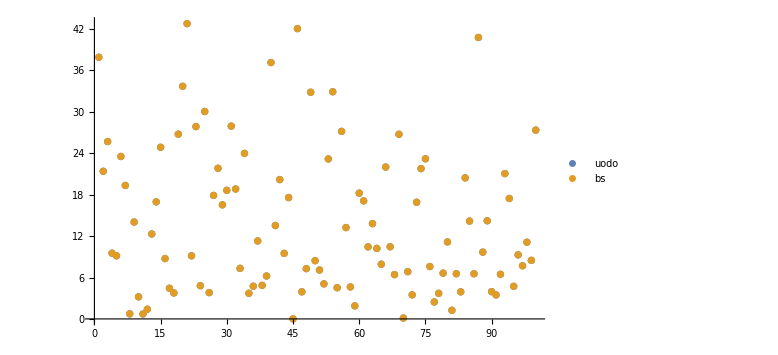

```mathematica
ListPlot[{Select[out[[2;;, -2]], NumericQ[#] &], Select[out[[2;;, -1]], NumericQ[#] &]},PlotRange->All, Filling->{1->{2}}, PlotLegends->Placed[{"uodo", "bs"}, {Right, Top}], ImageSize->Large]
```

```mathematica
TableForm[Reverse[SortBy[{Sequence@@#, #[[-2]]-#[[-1]]} & /@ out[[2;;]], Abs[#[[-1]]] &]][[1;;5]], TableHeadings->{None, {"call_put","type","S","X","sigma","T","intRate","yield", "uodo", "bs", "uodo-bs"}}]
```

call_put | type | S | X | sigma | T | intRate | yield | uodo | bs | uodo-bs
call | vanilla | 136.274 | 137.186 | 0.977098 | 0.711247 | 0.0162669 | 0.0273255 | 42.0658 | 42.0659 | -0.000184355
call | vanilla | 89.3859 | 92.0498 | 0.934701 | 0.764288 | 0.0136553 | 0.00940441 | 27.3575 | 27.3575 | -6.8076×10^-6
call | vanilla | 114.428 | 111.079 | 0.873019 | 0.700975 | 0.00509812 | 0.00571744 | 33.708 | 33.708 | -9.41098×10^-7
call | vanilla | 104.332 | 100.845 | 0.96243 | 0.568003 | 0.0421278 | 0.0432602 | 30.05 | 30.05 | -2.90437×10^-7
call | vanilla | 129.324 | 130.712 | 0.983817 | 0.456363 | 0.0415686 | 0.0311233 | 32.9158 | 32.9158 | -6.6261×10^-8

## Single

```mathematica
data=Import["C:\\Users\\fsiano\\work\\dev\\workspace\\BarrierOption\\TestData\\test_haug_single.csv"];
```

```mathematica
Select[data, #[[3]]≠#[[5]] &]
```

{{call_put,type,S,X,B,sigma,T,r,b,rebate,value},{call,do,100,90,95,0.25,0.5,0.08,0.04,3,9.0246},{call,do,100,100,95,0.25,0.5,0.08,0.04,3,6.7924},{call,do,100,110,95,0.25,0.5,0.08,0.04,3,4.8759},{call,uo,100,90,105,0.25,0.5,0.08,0.04,3,2.6789},{call,uo,100,100,105,0.25,0.5,0.08,0.04,3,2.358},{call,uo,100,110,105,0.25,0.5,0.08,0.04,3,2.3453},{call,do,100,90,95,0.3,0.5,0.08,0.04,3,8.8334},{call,do,100,100,95,0.3,0.5,0.08,0.04,3,7.0285},{call,do,100,110,95,0.3,0.5,0.08,0.04,3,5.4137},{call,uo,100,90,105,0.3,0.5,0.08,0.04,3,2.6341},{call,uo,100,100,105,0.3,0.5,0.08,0.04,3,2.4389},{call,uo,100,110,105,0.3,0.5,0.08,0.04,3,2.4315},{put,do,100,90,95,0.25,0.5,0.08,0.04,3,2.2798},{put,do,100,100,95,0.25,0.5,0.08,0.04,3,2.2947},{put,do,100,110,95,0.25,0.5,0.08,0.04,3,2.6252},{put,uo,100,90,105,0.25,0.5,0.08,0.04,3,3.776},{put,uo,100,100,105,0.25,0.5,0.08,0.04,3,5.4932},{put,uo,100,110,105,0.25,0.5,0.08,0.04,3,7.5187},{put,do,100,90,95,0.3,0.5,0.08,0.04,3,2.417},{put,do,100,100,95,0.3,0.5,0.08,0.04,3,2.4258},{put,do,100,110,95,0.3,0.5,0.08,0.04,3,2.6246},{put,uo,100,90,105,0.3,0.5,0.08,0.04,3,4.2293},{put,uo,100,100,105,0.3,0.5,0.08,0.04,3,5.8032},{put,uo,100,110,105,0.3,0.5,0.08,0.04,3,7.5649},{call,di,100,90,95,0.25,0.5,0.08,0.04,3,7.7627},{call,di,100,100,95,0.25,0.5,0.08,0.04,3,4.0109},{call,di,100,110,95,0.25,0.5,0.08,0.04,3,2.0576},{call,ui,100,90,105,0.25,0.5,0.08,0.04,3,14.1112},{call,ui,100,100,105,0.25,0.5,0.08,0.04,3,8.4482},{call,ui,100,110,105,0.25,0.5,0.08,0.04,3,4.591},{call,di,100,90,95,0.3,0.5,0.08,0.04,3,9.0093},{call,di,100,100,95,0.3,0.5,0.08,0.04,3,5.137},{call,di,100,110,95,0.3,0.5,0.08,0.04,3,2.8517},{call,ui,100,90,105,0.3,0.5,0.08,0.04,3,15.2098},{call,ui,100,100,105,0.3,0.5,0.08,0.04,3,9.7278},{call,ui,100,110,105,0.3,0.5,0.08,0.04,3,5.835},{put,di,100,90,95,0.25,0.5,0.08,0.04,3,2.9586},{put,di,100,100,95,0.25,0.5,0.08,0.04,3,6.5677},{put,di,100,110,95,0.25,0.5,0.08,0.04,3,11.9752},{put,ui,100,90,105,0.25,0.5,0.08,0.04,3,1.4653},{put,ui,100,100,105,0.25,0.5,0.08,0.04,3,3.3721},{put,ui,100,110,105,0.25,0.5,0.08,0.04,3,7.0846},{put,di,100,90,95,0.3,0.5,0.08,0.04,3,3.8769},{put,di,100,100,95,0.3,0.5,0.08,0.04,3,7.7989},{put,di,100,110,95,0.3,0.5,0.08,0.04,3,13.3078},{put,ui,100,90,105,0.3,0.5,0.08,0.04,3,2.0658},{put,ui,100,100,105,0.3,0.5,0.08,0.04,3,4.4226},{put,ui,100,110,105,0.3,0.5,0.08,0.04,3,8.3686}}

```mathematica
doubleKnockOutOutsideBarrierOptionValue[cp_,{sUnd_,sYield_,sVol_},{bUnd_,bYield_,bVol_},corr_,intRate_,{t1_,t2_,bLow_,bHigh_},strike_,t_,ts_,{nMin_,nMax_}]
```

```mathematica
"BarrierDownOut"
```

```mathematica
FinancialDerivative[{btype,"European",callput},{"StrikePrice"->x,"Expiration"->bigT,"Barrier"->b, "Rebate"->rebate},{"CurrentPrice"->s,"Dividend"->q,"Volatility"->sigma,"InterestRate"->r}]
```

```mathematica
Remove[checkSingle]
checkSingle[callput_,type_,s_,x_,barrier_,sigma_,bigT_,intRate_,b_,rebate_,value_]:=
Module[{corr, nMin, nMax, cp},
corr=0.999;
nMin=-2;
nMax=2;
cp=If[callput=="call", {1, "Call"}, {-1, "Put"}];
Which[
type=="do", {FinancialDerivative[{"BarrierDownOut","European", cp[[2]]},{"StrikePrice"->x,"Expiration"->bigT,"Barrier"->barrier, "Rebate"->0},{"CurrentPrice"->s,"Dividend"->intRate-b,"Volatility"->sigma,"InterestRate"->intRate}], doubleKnockOutOutsideBarrierOptionValue[cp[[1]],{s,intRate-b,sigma},{s,intRate-b,sigma},corr,intRate,{10^-3,bigT,barrier,10^4},x,bigT, bigT,{nMin, nMax}]}, 
type=="uo",{FinancialDerivative[{"BarrierUpOut","European",cp[[2]]},{"StrikePrice"->x,"Expiration"->bigT,"Barrier"->barrier, "Rebate"->0},{"CurrentPrice"->s,"Dividend"->intRate-b,"Volatility"->sigma,"InterestRate"->intRate}], doubleKnockOutOutsideBarrierOptionValue[cp[[1]],{s,intRate-b,sigma},{s,intRate-b,sigma},corr,intRate,{10^-3,bigT,10^-4, barrier},x,bigT, bigT,{nMin, nMax}]}, 
type=="di",{FinancialDerivative[{"BarrierDownIn","European",cp[[2]]},{"StrikePrice"->x,"Expiration"->bigT,"Barrier"->barrier, "Rebate"->0},{"CurrentPrice"->s,"Dividend"->intRate-b,"Volatility"->sigma,"InterestRate"->intRate}],doubleKnockOutOutsideBarrierOptionValue[cp[[1]],{s,intRate-b,sigma},{s,intRate-b,sigma},corr,intRate,{10^-3,bigT,10^-4, 10^4},x,bigT, bigT,{nMin, nMax}]-doubleKnockOutOutsideBarrierOptionValue[cp[[1]],{s,intRate-b,sigma},{s,intRate-b,sigma},corr,intRate,{10^-3,bigT,barrier, 10^4},x,bigT, bigT,{nMin, nMax}]}, 
type=="ui",{FinancialDerivative[{"BarrierUpIn","European",cp[[2]]},{"StrikePrice"->x,"Expiration"->bigT,"Barrier"->barrier, "Rebate"->0},{"CurrentPrice"->s,"Dividend"->intRate-b,"Volatility"->sigma,"InterestRate"->intRate}],doubleKnockOutOutsideBarrierOptionValue[cp[[1]],{s,intRate-b,sigma},{s,intRate-b,sigma},corr,intRate,{10^-3,bigT,10^-4, 10^4},x,bigT, bigT,{nMin, nMax}]-doubleKnockOutOutsideBarrierOptionValue[cp[[1]],{s,intRate-b,sigma},{s,intRate-b,sigma},corr,intRate,{10^-3,bigT,10^-4, barrier},x,bigT, bigT,{nMin, nMax}]}
]
]
```

```mathematica
out={Sequence@@#, Sequence@@checkSingle[Sequence@@#]} & /@ Select[data[[2;;]], #[[3]]≠#[[5]] &];
```

```mathematica
TableForm[out, TableHeadings->{Range[Length[out]], {"call_put","type","S","X", "B","sigma","T","intRate","b", "rebate", "Haug", "WL","FS"}}]
```

| call_put | type | S | X | B | sigma | T | intRate | b | rebate | Haug | WL | FS
1 | call | do | 100 | 90 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 9.0246 | 6.74473 | 6.74057
2 | call | do | 100 | 100 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 6.7924 | 4.5126 | 4.50944
3 | call | do | 100 | 110 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 4.8759 | 2.59602 | 2.59441
4 | call | uo | 100 | 90 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.6789 | 0.333564 | 0.336
5 | call | uo | 100 | 100 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.358 | 0.0126708 | 0.0136423
6 | call | uo | 100 | 110 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.3453 | 0. | 2.67017×10^-15
7 | call | do | 100 | 90 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 8.8334 | 6.41637 | 6.41195
8 | call | do | 100 | 100 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 7.0285 | 4.61155 | 4.608
9 | call | do | 100 | 110 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 5.4137 | 2.99671 | 2.99459
10 | call | uo | 100 | 90 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.6341 | 0.202509 | 0.20471
11 | call | uo | 100 | 100 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.4389 | 0.00740921 | 0.0082369
12 | call | uo | 100 | 110 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.4315 | 0. | 1.01187×10^-12
13 | put | do | 100 | 90 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.2798 | 0. | -4.07057×10^-15
14 | put | do | 100 | 100 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.2947 | 0.0149117 | 0.0159147
15 | put | do | 100 | 110 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.6252 | 0.345376 | 0.347928
16 | put | uo | 100 | 90 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 3.776 | 1.43061 | 1.42966
17 | put | uo | 100 | 100 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 5.4932 | 3.14788 | 3.14547
18 | put | uo | 100 | 110 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 7.5187 | 5.17337 | 5.16999
19 | put | do | 100 | 90 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.417 | 0. | 4.90362×10^-15
20 | put | do | 100 | 100 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.4258 | 0.00881952 | 0.00968517
21 | put | do | 100 | 110 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.6246 | 0.207617 | 0.209911
22 | put | uo | 100 | 90 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 4.2293 | 1.7977 | 1.79641
23 | put | uo | 100 | 100 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 5.8032 | 3.37172 | 3.36905
24 | put | uo | 100 | 110 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 7.5649 | 5.13342 | 5.12993
25 | call | di | 100 | 90 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 7.7627 | 7.08856 | 7.09271
26 | call | di | 100 | 100 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 4.0109 | 3.33683 | 3.33998
27 | call | di | 100 | 110 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.0576 | 1.3835 | 1.3851
28 | call | ui | 100 | 90 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 14.1112 | 13.4997 | 13.4973
29 | call | ui | 100 | 100 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 8.4482 | 7.83676 | 7.83579
30 | call | ui | 100 | 110 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 4.591 | 3.97952 | 3.97952
31 | call | di | 100 | 90 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 9.0093 | 8.46525 | 8.46967
32 | call | di | 100 | 100 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 5.137 | 4.59295 | 4.59649
33 | call | di | 100 | 110 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.8517 | 2.30759 | 2.30971
34 | call | ui | 100 | 90 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 15.2098 | 14.6791 | 14.6769
35 | call | ui | 100 | 100 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 9.7278 | 9.19709 | 9.19626
36 | call | ui | 100 | 110 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 5.835 | 5.3043 | 5.3043
37 | put | di | 100 | 90 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 2.9586 | 2.28447 | 2.28447
38 | put | di | 100 | 100 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 6.5677 | 5.89359 | 5.89259
39 | put | di | 100 | 110 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 11.9752 | 11.3011 | 11.2986
40 | put | ui | 100 | 90 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 1.4653 | 0.853863 | 0.854811
41 | put | ui | 100 | 100 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 3.3721 | 2.76063 | 2.76304
42 | put | ui | 100 | 110 | 105 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 7.0846 | 6.47312 | 6.4765
43 | put | di | 100 | 90 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 3.8769 | 3.3328 | 3.3328
44 | put | di | 100 | 100 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 7.7989 | 7.25475 | 7.25389
45 | put | di | 100 | 110 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 13.3078 | 12.7637 | 12.7614
46 | put | ui | 100 | 90 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 2.0658 | 1.5351 | 1.5364
47 | put | ui | 100 | 100 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 4.4226 | 3.89185 | 3.89452
48 | put | ui | 100 | 110 | 105 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 8.3686 | 7.83785 | 7.84135

```mathematica
out[[1;;2]]
```

{{call,do,100,90,95,0.25,0.5,0.08,0.04,3,9.0246,6.74473,6.74057},{call,do,100,100,95,0.25,0.5,0.08,0.04,3,6.7924,4.5126,4.50944}}

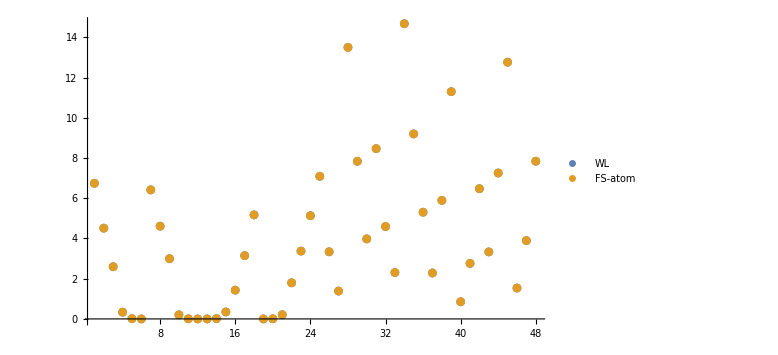

```mathematica
ListPlot[{out[[All, -2]], out[[All, -1]]}, PlotRange->All, Filling->{1->{2}}, PlotLegends->Placed[{"WL", "FS-atom"}, {Right, Top}], ImageSize->Large]
```

```mathematica
TableForm[Reverse[SortBy[{Sequence@@#, #[[-2]]-#[[-1]]} & /@ out, Abs[#[[-1]]] &]][[1;;5]], TableHeadings->{None, {"call_put","type","S","X", "B","sigma","T","intRate","b", "rebate", "Haug (with rebate)", "WL (no rebate)","FS (no rebate)", "WL - FS"}}]
```

call_put | type | S | X | B | sigma | T | intRate | b | rebate | Haug (with rebate) | WL (no rebate) | FS (no rebate) | WL - FS
call | do | 100 | 90 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 8.8334 | 6.41637 | 6.41195 | 0.00441261
call | di | 100 | 90 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 9.0093 | 8.46525 | 8.46967 | -0.00441261
call | di | 100 | 90 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 7.7627 | 7.08856 | 7.09271 | -0.00415685
call | do | 100 | 90 | 95 | 0.25 | 0.5 | 0.08 | 0.04 | 3 | 9.0246 | 6.74473 | 6.74057 | 0.00415685
call | di | 100 | 100 | 95 | 0.3 | 0.5 | 0.08 | 0.04 | 3 | 5.137 | 4.59295 | 4.59649 | -0.0035469